```mathematica
ClearAll["Global`*"]
Get[NotebookDirectory[]<>"../src/MultipleScattering2D.wl"];
```

## Impulse in time from receiver

AcousticImpulse

{δω,Ω}: {1.39626,27.9253}

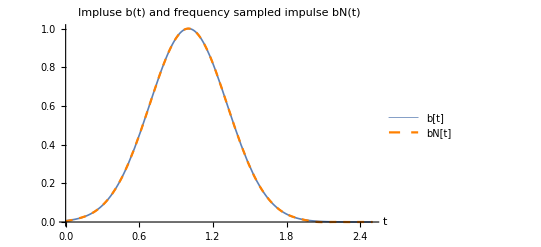

```mathematica
AcousticImpulse
b1[τ_]= ⅇ^(-5(τ-1)^2);
Plot[b1[τ],{τ,0,3}];
options=Sequence["Impulse"-> b1,"ImpulsePeriod"->2.,"PrintChecks"-> True,"Boundary"-> "Neumann","FrequencyModes"->20,"NAngularModes"->7];
txθxrxwI= AcousticImpulse[0.5,{2.5,0.1},options];
(*Usage*)
(*AcousticImpulse[t,{Subscript[R, max],δR}]*)
(*AcousticImpulse[t]*)
```

Max Amp: 0.0999416

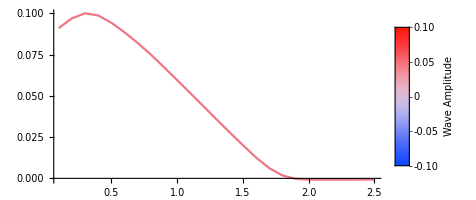

```mathematica
(*For just one time t0 and using scattering coefficients*)
ClearAll[wFθ]
t0=2.;
(*angular frequencies*)
rngω=Range[-15,15,0.05];
(*Distance from source*)
rngr=Range[0.1,2.5,0.1];
(*Hankel orders*)
rngn={0};
(*For a Green's function impulse*)
sourceCoefficients =  Outer[ ⅈ/4 KroneckerDelta[#1]+0#2&,rngn,rngω] ;
(*Return a function of θ, which for each θ gives a list {{Subscript[r, 0],Subscript[w, 0]},...,{Subscript[r, n],Subscript[w, n]}}; *)
wFθ=WaveFθFromCoefficients[sourceCoefficients,rngω,t0,rngr];
p=PlotWaves[wFθ[0.2]]
```

{δω,Ω}: {0.890309,17.8062}

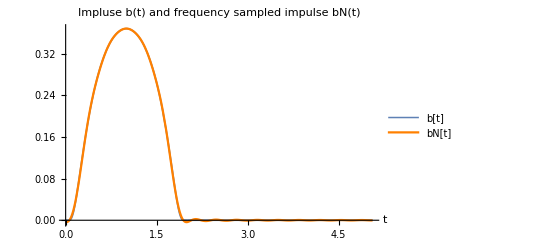

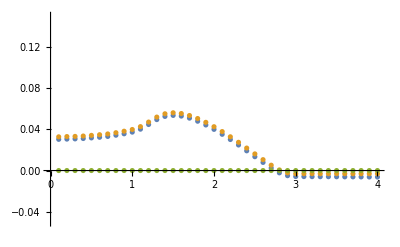

{δω,Ω}: {0.890309,17.8062}

-Graphics-

-Graphics-

```mathematica
test WaveFromCoefficients by generating an impulse;

(*Chooose angular frequency rngω*)
	maxω=20.; 
	Nω= 21; 
	δω=maxω/Nω;
	δ=0.5 δω;
	rngω = Range[0, maxω-δ,δω];
	rngωFourier=  rngω~Join~Reverse@Drop[-rngω,1] +δ;

(*Specify the green's function as the source*)
	(*Number of hankel functions, only Subscript[H, 0]^(1) is needed so*)
	rngn={0}; 
	source = ⅈ/4 KroneckerDelta[#1]+0#2 &;
	sourceCoefficients =  Outer[source,rngn,rngωFourier];

(*Mesh in cylindrical coordiantes*)
	rngr=Range[0.1,4.,0.1];
	rngθ= Range[0,π+0.1,.1];

(*Calculate wave in frequency*)
	listWave= listWaveFromCoefficients[sourceCoefficients,rngωFourier,rngθ,rngr];

(*choose a time t0*)	
         n= Round[Length[listWave]/2];
	t0 = listWave[[n]][[1,1,1]];

(*Compare with Impulse*)
	options=Sequence["PrintChecks"-> True];
	listwIOr= AcousticImpulse[t0,{Max@rngr,rngr[[2]]-rngr[[1]]},options];
	ListPlot[{Re@#,listwIOr,{#ᵀ[[1]],Im@#ᵀ[[2]]}ᵀ},PlotRange->{-0.05,0.15}]&@Transpose[{#[[3]],#[[4]]}]&@Transpose[listWave[[n,1]]]
```